# Intro to Mathematica

## The basics

#### Cells

All operations are divided into “cells” within a “notebook”

New cells are added by either:

Clicking in an area where the cursor appears horizontal

Pressing the “<Down arrow>” key at the end of the current cell, or the “<Up arrow>” key at the beginning

This produces a horizontal line. Click the “Plus” symbol to enter a cell-selection menu. The default is “Mathematica input”.

To evalute a cell, type "<Shift> + <Enter>"

Output from a given line can be suppressed with a semicolon

The previous output can be referenced with %

```mathematica
2+2*4
% / 15
N[%]
```

10

2/3

0.666667

We see the N[] function returns the numeric value of its argument

Multiple lines may be combined into one cell

```mathematica
(* Fun fact: this is how you can comment your notebook *)
a=2;
b=2*a;
c=a+b
```

6

A final note: the nested structure of the cells is illustrated on the far right of the notebook. Double-clicking collapses the selected cell.

### Brackets: (), [], {}

Each of these three brackets has a specific role in Mathematica:

() - used to specify operator precedence and group mathematical expressions

```mathematica
w=(-2+4)^((2+4/2)/(3+1))
```

2

[] - used to specify function arguments

```mathematica
N[99/100]
```

0.99

```mathematica
Factorial[5]
```

120

Note that if function suggestions are not automatically generated as you type, press “<Ctrl> + <k>” to view a list of functions that begin with a given string of letters

Additionally, pressing “<Ctrl> + <Shift> + <k>” will provide an argument list template. Press “<Tab>” to quickly navigate through the arguments. For example, after typing Plot, “<Ctrl> + <Shift> + <k>” will give: Plot[f,{x,x_min,x_max}]

{} - used to generate lists

```mathematica
v={1, -2, 15/2};
q=2*v
```

{2,-4,15}

### Free-form input

Press “<=>” when creating a new cell to enter a free-form input mode, sending commands to Wolfram|Alpha for interpretation. Alternatively, select “Free-form input” from the cell-selection menu

Useful for trying out commands and finding proper syntax

Output can be expanded, and commands selected and reused

WolframAlphaQueryResults

-Graphics3D-

WolframAlphaQueryResults

{{y[t]→ⅇ^t C[1]+ⅇ^-t C[2]-Sin[t]/2}}

## Operating with user-defined functions

### Creating new functions

Use the following general syntax to define and evaluate new functions:

```mathematica
f1[x_] := Sin[x] + Exp[x] - x^2;
f1[Pi]
```

ⅇ^π-π^2

Note the x_ and :=

Multivariable functions are created similarly

```mathematica
f1[x_] := Sin[x] + Exp[x] - x^2;
f2[x_, y_, z_] := f1[x] - Exp[x] + y*z;
f2[Pi, 1, 2]
```

2-π^2

### Differentiation

Differentiate a previously defined function with the following command:

Note you must specify D[f[x], x]. The simpler input D[f, x] will not work.

```mathematica
f[x_] := x^3 + Sin[x];
D[f[x], x]
```

3 x^2+Cos[x]

You can also define the expression directly in the argument list:

```mathematica
D[Exp[2*x], x]
```

2 ⅇ^(2 x)

Higher derivatives are found through the following syntax: D[f[x], {x,n}]

```mathematica
D[ArcTan[x], {x,4}]
```

-(48 x^3)/((1+x^2)^4)+(24 x)/((1+x^2)^3)

```mathematica
Simplify[%]
```

-(24 x (-1+x^2))/((1+x^2)^4)

### Integration

Integration is similarly defined, although we now have the option to specify limits

Note the lack of an integration constant in the solution

1/2 ⅇ^x (-Cos[x]+Sin[x])

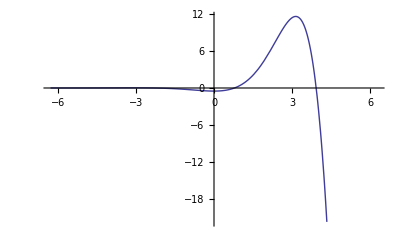

```mathematica
sol=Integrate[Sin[x]*Exp[x], x]
Plot[sol, {x, -2*Pi, 2*Pi}]
```

```mathematica
Integrate[2*Sin[x] + 1, {x, 0, 2*Pi}]
```

2 π

## Solving differential equations

### Analytical solutions

The DSolve[] command analytically solves differential equations with the following syntax: DSolve[{eqn1, eqn2, ..., init_cond1, init_cond2, ...},{dependent_var1, dependent_var2, ...},independent_var]

We must use a new syntax to define equations (as opposed to functions, which used :=). To create an equation, type ==. This is exhibited in the following:

{{F[t]→1/4 (4 Cos[t]-2 t Cos[t]+2 Sin[t]-2 Cos[t]^2 Sin[t]+Cos[t] Sin[2 t])}}

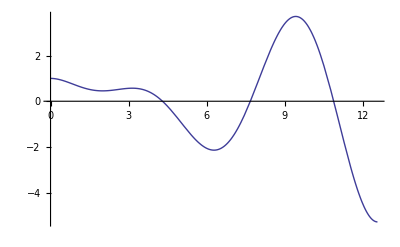

```mathematica
sol = DSolve[{F''[t] + F[t] == Sin[t], F'[0]==0, F[0]==1}, {F[t]}, t]
Plot[F[t] /. sol, {t, 0, 4*Pi}]
```

The /. used in the Plot[] command above is the replacement operator, which basically creates a rule saying sol will be used in place of F[t]

We can also use the D[] command we learned previously to specify differential equations

```mathematica
DSolve[{D[y[t], t]==x[t], D[x[t], t]==y[t], y[0]==1, x[0]==1}, {y[t], x[t]}, t]
```

{{x[t]→ⅇ^t,y[t]→ⅇ^t}}

### Numerical solutions

The NDSolve[] command provides numerical solutions with a syntax very similar to DSolve[], except that the interval of integration must be specified:

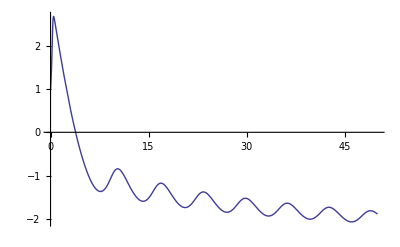

```mathematica
sol = NDSolve[{y'[t]==Exp[y[t]]*Sin[y[t] + t], y[0]==1}, {y[t]}, {t, 0, 50}];
Plot[Evaluate[y[t] /. sol], {t, 0, 50}, PlotRange->Full]
```

Evaluate[] is now required as we lack an exact symbolic expression for y[t]. Also, the plot parameter PlotRange is specified as Full. The alternative produces

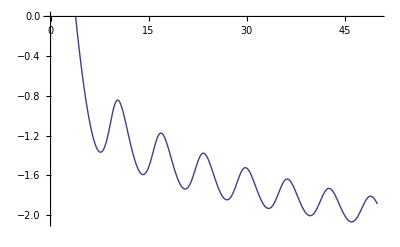

```mathematica
Plot[Evaluate[y[t] /. sol], {t, 0, 50}]
```

## Plotting examples

#### 2D plots

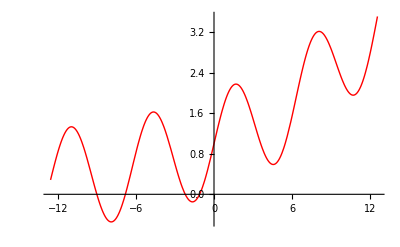

```mathematica
Plot[y[x]=Sin[x]+Exp[x/10], {x, -4Pi, 4Pi}, PlotStyle->Red]
```

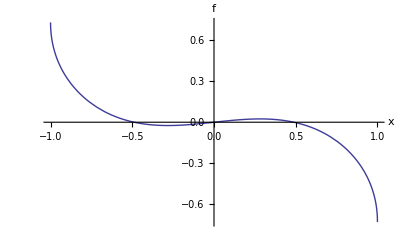

```mathematica
f[x_] := Erf[x]-ArcSin[x];
Plot[f[x], {x, -1, 1}, PlotRange->Full, AxesLabel->{x, f}]
```

#### 3D plots

```mathematica
Plot3D[Sin[x] + Exp[y], {x, -Pi, Pi}, {y, -1, 1}, AxesLabel->{x, y, Temp}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x]Cos[y], {x, -Pi, Pi}, {y, -Pi, Pi}, PlotLabel->Sin[x]Cos[y]]
```

-Graphics3D-

#### Contour plots

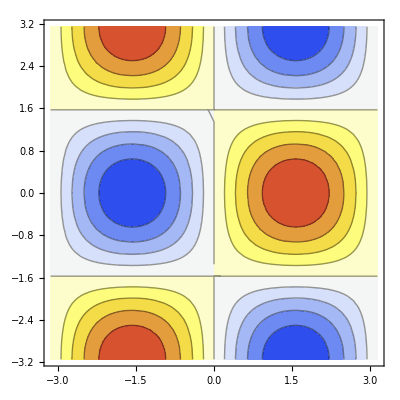

```mathematica
ContourPlot[Sin[x]Cos[y], {x, -Pi, Pi}, {y, -Pi, Pi}, ColorFunction->ColorData["TemperatureMap"]]
```

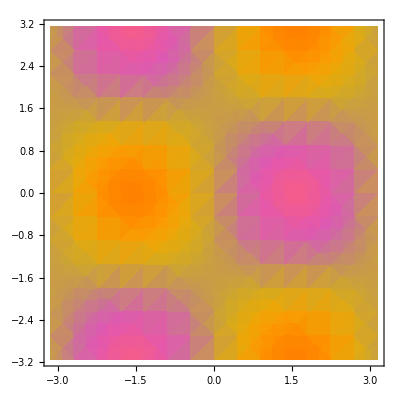

```mathematica
DensityPlot[Sin[x]Cos[y], {x, -Pi, Pi}, {y, -Pi, Pi}, ColorFunction->ColorData["FruitPunchColors"]]
```

#### Vector fields

The first argument specifies first the x-contribution to the slope at each point, then the the y-contribution

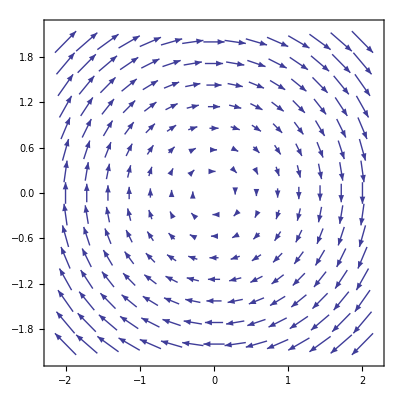

```mathematica
VectorPlot[{y,-x}, {x,-2,2}, {y,-2,2}]
```

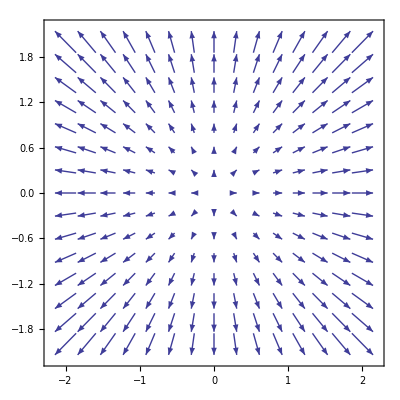

```mathematica
VectorPlot[{x, y}, {x, -2, 2}, {y, -2, 2}]
```

## Other

This tutorial has covered the basic tools used to interact with Mathematica. For more information on any Mathematica function, click “Help -> Documentation Center”. Here you will find detailed information on each method, with interactive examples embedded throughout.

If you're positive you've entered your code correctly and continue to run into variable errors, consider using the Remove[] command: Remove[symbol_1,…]

This entirely removes the listed variables from Mathematica, allowing them to be reused

The “Undo” command, “<Ctrl> + <z>” is horribly broken. Additionally, there is not, to my knowledge, a “Redo”/”<Ctrl> + <y>” command. To combat this unfortunate circumstance, save very, very often.